```mathematica
data=Import["/afs/cs.hm.edu/users/ifs13028/cg/prakt1/haskell-test-with-nubBy/haskell-times-sec.csv"]
```

{{10;0m0.005s;0.005},{20;0m0.007s;0.007},{30;0m0.011s;0.011},{40;0m0.019s;0.019},{50;0m0.043s;0.043},{60;0m0.079s;0.079},{70;0m0.142s;0.142},{80;0m0.240s;0.24},{90;0m0.380s;0.38},{100;0m0.595s;0.595},{110;0m0.898s;0.898},{120;0m1.291s;1.291},{130;0m1.827s;1.827},{140;0m2.520s;2.52},{150;0m3.350s;3.35},{160;0m4.337s;4.337},{170;0m5.149s;5.149},{180;0m6.378s;6.378},{190;0m7.665s;7.665},{200;0m8.315s;8.315},{220;0m12.230s;12.23},{240;0m17.284s;17.284},{260;0m23.987s;23.987},{280;0m32.974s;32.974},{300;0m42.168s;42.168},{350;1m26.870s;86.87},{400;2m15.083s;135.083},{450;3m42.443s;222.443},{500;5m52.218s;352.218}}

```mathematica
d2=StringSplit[#[[1]],";"]&/@data
```

{{10,0m0.005s,0.005},{20,0m0.007s,0.007},{30,0m0.011s,0.011},{40,0m0.019s,0.019},{50,0m0.043s,0.043},{60,0m0.079s,0.079},{70,0m0.142s,0.142},{80,0m0.240s,0.24},{90,0m0.380s,0.38},{100,0m0.595s,0.595},{110,0m0.898s,0.898},{120,0m1.291s,1.291},{130,0m1.827s,1.827},{140,0m2.520s,2.52},{150,0m3.350s,3.35},{160,0m4.337s,4.337},{170,0m5.149s,5.149},{180,0m6.378s,6.378},{190,0m7.665s,7.665},{200,0m8.315s,8.315},{220,0m12.230s,12.23},{240,0m17.284s,17.284},{260,0m23.987s,23.987},{280,0m32.974s,32.974},{300,0m42.168s,42.168},{350,1m26.870s,86.87},{400,2m15.083s,135.083},{450,3m42.443s,222.443},{500,5m52.218s,352.218}}

```mathematica
d3=ToExpression[#]&/@d2
```

{{10,0.,0.005},{20,0.,0.007},{30,0.,0.011},{40,0.,0.019},{50,0.,0.043},{60,0.,0.079},{70,0.,0.142},{80,0.,0.24},{90,0.,0.38},{100,0.,0.595},{110,0.,0.898},{120,0.,1.291},{130,0.,1.827},{140,0.,2.52},{150,0.,3.35},{160,0.,4.337},{170,0.,5.149},{180,0.,6.378},{190,0.,7.665},{200,0.,8.315},{220,0.,12.23},{240,0.,17.284},{260,0.,23.987},{280,0.,32.974},{300,0.,42.168},{350,0.87 m26 s,86.87},{400,0.166 m15 s,135.083},{450,1.329 m42 s,222.443},{500,1.09 m52 s,352.218}}

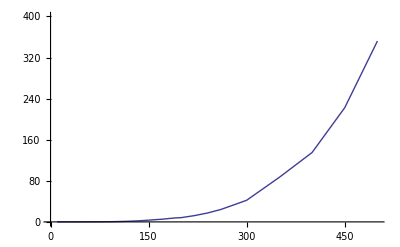

```mathematica
ListLinePlot[d3[[All,{1,3}]],PlotRange->{{0,500},{0,400}}]
```